```mathematica
（* y=f(x)  2D ,Plot,ListPlot 
z=f(x,y) 3D,Plot3D,ContourPlot,DensityPlot 
s=f(x,y,z) 4D,ContourPlot3D 
orbtal-like futns:f(x,y,z)=Ag(r)h(x,y,z) ,r=(x^2+y^2+z^2)^0.5
               g                     h
1s        e^-r              1
2pz     e^(-r/2)    z
3dz2  e^(-r/3)    3z^2-r^2 *)
```

```mathematica
r[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
f[x_,y_,z_]:=E^-r[x,y,z];
ContourPlot3D[f[x,y,z]==0.05,{x,-3,3},{y,-3,3},{z,-3,3},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
f[x_,y_,z_]:=z*E^(-r[x,y,z]/2);
ContourPlot3D[f[x,y,z]==0.1,{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
f[x_,y_,z_]:=z*E^(-r[x,y,z]/2);
ContourPlot3D[{f[x,y,z]==0.1,f[x,y,z]==-0.1},{x,-10,10},{y,-10,10},{z,-10,10},AxesLabel->{"x","y","z"},Mesh->None,ContourStyle->{Directive[Green,Specularity[White,100]],Directive[Yellow,Specularity[White,100]]}]
```

```mathematica
f[x_,y_,z_]:=(3*z^2-r[x,y,z]^2)*E^(-r[x,y,z]/3);
ContourPlot3D[{f[x,y,z]==0.1,f[x,y,z]==-0.1},{x,-30,30},{y,-30,30},{z,-30,30},AxesLabel->{"x","y","z"},Mesh->None,ContourStyle->{Directive[Green,Specularity[White,100]],Directive[Yellow,Specularity[White,100]]}]
```

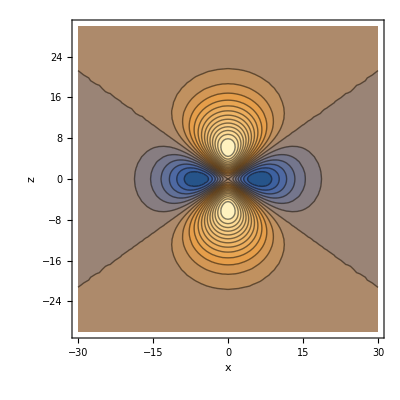

```mathematica
r[x_,z_]:=Sqrt[x^2+z^2];
f[x_,z_]:=(3*z^2-r[x,z]^2)*E^(-r[x,z]/3);
ContourPlot[{f[x,z]},{x,-30,30},{z,-30,30},FrameLabel->{"x","z"},PlotRange->All,Contours->20]
```

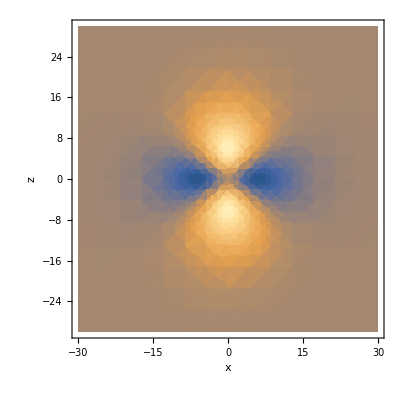

```mathematica
DensityPlot[{f[x,z]},{x,-30,30},{z,-30,30},FrameLabel->{"x","z"},PlotRange->All]
```